# r_out

```mathematica
<<SpinWeightedSpheroidalHarmonics`
Clear[M,l,m,a,r0,rpos,ω,rp,rm,λ]
r1[x_]:=1-2M x+a^2 x^2
r2[x_]:=(2M x^2-2 a^2 x^3)(1-2M x+a^2 x^2)//Expand
W[x_]:=(((r^2+a^2)ω-a m)/r^2)^2-(r^2-2M r+a^2)/r^4(λ-2a m ω+a^2 ω^2+(2(M r-a^2))/r^2)/.{r->1/x}//Expand
Wout[r_]:=(((r^2+a^2)ω-a m)/r^2)^2-(r^2-2M r+a^2)/r^4(λ-2a m ω+a^2 ω^2+(2(M r-a^2))/r^2);
Δ[r_]:=r^2-2M r+a^2
```

```mathematica
(coeffsoverxk=CoefficientList[k(k+1)r1[x]^2 x^2-(2ⅈ ω k r1[x]+k r2[x])x^1+(W[x]-ω^2)//Expand,x]);
(Fs = Table[coeffsoverxk[[i+1]]/.{k->k-i+1},{i,1,6}]//Simplify)//MatrixForm
```

(-2 ⅈ k ω
-1+(-1+k)^2+k-λ+4 ⅈ (-1+k) M ω+a^2 ω^2
-2 ⅈ a^2 (-2+k) ω+2 M (-3+5 k-2 k^2+λ-2 a m ω+a^2 ω^2)
4 (-2+k)^2 M^2+a^2 (8-8 k+2 k^2+m^2-λ)
-2 a^2 (15-11 k+2 k^2) M
a^4 (12-7 k+k^2))

```mathematica
f0[n_]:= -2 ⅈ n ω
f1[n_]:=n^2-λ+ω (-4 ⅈ M+a^2 ω)+n (-1+4 ⅈ M ω)
f2[n_]:=-2 ⅈ a^2 (-2+n) ω+2 M (-3+5 n-2 n^2+λ-2 a m ω+a^2 ω^2)
f3[n_]:=4 M^2 (-2+n)^2+a^2 (8+m^2-8 n+2 n^2-λ)
f4[n_]:=-2 a^2 M (15-11 n+2 n^2)
f5[n_]:=a^4 (12-7 n+n^2)
fi[n_]:={f0[n],f1[n],f2[n],f3[n],f4[n],f5[n]}
```

```mathematica
l=2;
m=2;
M=1;
r0=10M; (*Position of orbit*)
rpos = 10000M; (*Position of observer*)
a= (.9)M;
rp= M+√(M^2-a^2);
rm = M-√(M^2-a^2);
ω = m/M(M/r0)^(3/2)/(1+(a/M)(M/r0)^(3/2));
λ=SpinWeightedSpheroidalEigenvalue[0,l,m,a ω];

kout = 100;

cs = RecurrenceTable[{f0[k]c[k]+f1[k]c[k-1]+f2[k]c[k-2]+f3[k]c[k-3]+f4[k]c[k-4]+f5[k]c[k-5]==0,c[0]==1,c[-1]==0,c[-2]==0,c[-3]==0,c[-4]==0},c,{k,0,kout}];
```

```mathematica
rs[r_]:=r+M Log[Δ[r]/M^2]+(2 M^2-a^2)/(2 √(M^2-a^2))Log[(r-rp)/(r-rm)]
```

```mathematica
ψ[r_] := Exp[ⅈ ω rs[r]]Sum[cs[[k+1]] r^-k,{k,0,kout}];
```

```mathematica
Δ[r]/r^2(D[Δ[r]/r^2,r]D[ψ[r],r]+Δ[r]/r^2 D[ψ[r],{r,2}])+Wout[r]ψ[r]/.{r->rpos}
```

-1.73472×10^-18-4.33681×10^-19 ⅈ

```mathematica
ψ[rpos]
```

0.943108+0.332498 ⅈ

```mathematica
Initψout[l_,m_,kout_,a_,M_,r0_] := 
Module[{i = l, j= m , N=kout, s = a, Μ=M, ρ0 = r0,f0,f1,f2,f3,f4,f5,f6,n,ω,rp,rm,λ,Q = SpinWeightedSpheroidalEigenvalue},
rp= Μ+√(Μ^2-s^2);
rm = Μ-√(Μ^2-s^2);
ω = j/Μ(Μ/ρ0)^(3/2)/(1+(s/Μ)(Μ/ρ0)^(3/2));
λ = Q[0,i,j,s ω];
f0= -2 ⅈ n ω;
f1=n^2-λ+ω (-4 ⅈ Μ+s^2 ω)+n (-1+4 ⅈ Μ ω);
f2=-2 ⅈ s^2 (-2+n) ω+2Μ (-3+5 n-2 n^2+λ-2 s j ω+s^2 ω^2);
f3=4 Μ^2 (-2+n)^2+s^2 (8+j^2-8 n+2 n^2-λ);
f4=-2 a^2 Μ (15-11 n+2 n^2);
f5=s^4 (12-7 n+n^2);


cs = RecurrenceTable[{f0 c[n]+f1 c[n-1]+f2 c[n-2]+f3 c[n-3]+f4 c[n-4]+f5 c[n-5]==0,c[0]==1,c[-1]==0,c[-2]==0,c[-3]==0,c[-4]==0},c,{n,0,N}]
(*Exp[ⅈ ω (ρ+Μ Log[(ρ^2-2 Μ ρ +s^2)/Μ^2]+(2 Μ^2-s^2)/(2 √(Μ^2-s^2))Log[(ρ-rp)/(ρ-rm)])]Sum[cs[[n+1]] r^-n,{n,0,N}]*)
]
ψout[l_,m_,kout_,a_,M_,r0_,r_,c_]:=Exp[ⅈ (m/M(M/r0)^(3/2)/(1+(a/M)(M/r0)^(3/2))) (r+M Log[(r^2-2 M r +a^2)/M^2]+(2 M^2-a^2)/(2 √(M^2-a^2))Log[(r-M-√(M^2-a^2))/(r-M+√(M^2-a^2))])]Sum[c[[n+1]] r^-n,{n,0,kout}]
```

```mathematica
cList = Initψout[2,2,100,.9,1,10];
```

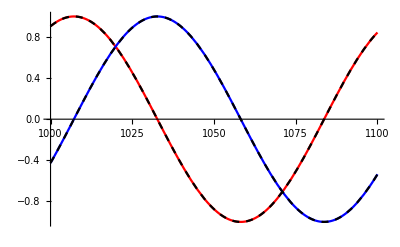

```mathematica
Show[
Plot[{Re[ψout[2,2,100,.9,1,10,r,cList]],Im[ψout[2,2,100,.9,1,10,r,cList ]]},{r,1000,1100},PlotStyle->{Red,Blue}],

Plot[{Re[ψ[r]],Im[ψ[r]]},{r,1000,1100},PlotStyle->{{Black,Dashed},{Black,Dashed}}]
]
```

```mathematica
ReIm[ψout[2,2,100,.1,1,10,100,cList]]
ReIm[ψout[2,2,100,.1,1,10,100,cList]]
```

{4.62898×10^45,-1.28626×10^46}

{4.62898×10^45,-1.28626×10^46}

```mathematica
hold = Table[ψout[2,2,n,.9,1,10,100,Initψout[2,2,n,.9,1,10]],{n,1,500}];
hold2 =  Table[ψout[2,2,n,.9,1,10,500,Initψout[2,2,n,.9,1,10]],{n,1,500}];
hold3 = Table[ψout[2,2,n,.9,1,10,1000,Initψout[2,2,n,.9,1,10]],{n,1,500}];
hold4 = Table[ψout[2,2,n,.9,1,10,10000,Initψout[2,2,n,.9,1,10]],{n,1,1000}];
```

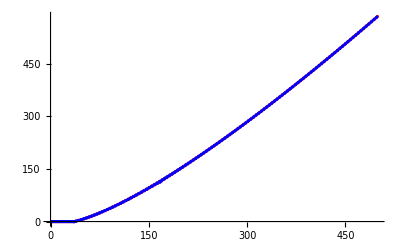

```mathematica
ListPlot[Log10[{Re[hold],Im[hold]}],PlotStyle->{Red,Blue}]
```

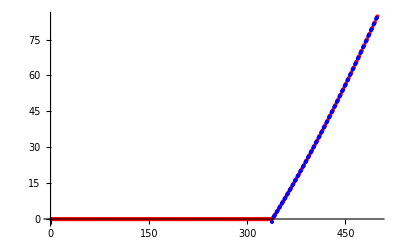

```mathematica
hold2 = Table[ψout[2,2,n,.9,1,10,10000,Initψout[2,2,n,.9,1,10]],{n,1,500}];
ListPlot[Log10[{Re[hold3],Im[hold3]}],PlotStyle->{Red,Blue}]
```

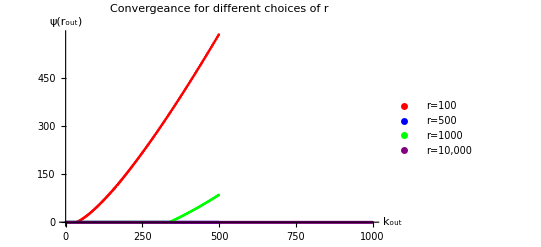

```mathematica
ListPlot[Log10[Re[{hold,hold2,hold3,hold4}]],PlotStyle->{Red,Blue,Green,Purple},PlotLegends->{"r=100","r=500","r=1000","r=10,000"},PlotLabel->"Convergeance for different choices of r",AxesLabel->{"k_out","ψ(r_out)"}]
```